## M=(1/t^* | -r^*/t^* -r/t | 1/t)

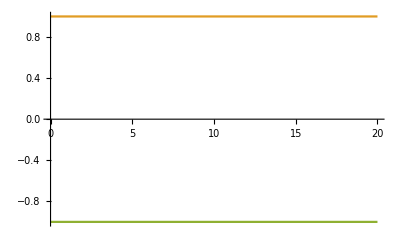

```mathematica
A = 3.84;
V = 13.6;
a = 5.0;
w = 3.0;
b = 2.0;
q= Sqrt[En/A];
β=Sqrt[(V-En)/A];
Plot[{Cosh[β*b]*Cos[q*w]-((q^2-β^2)/(2*q*β))*Sinh[β*b]*Sin[q*w],1, -1}, {En, 0, 20}]
```

```mathematica
Plot[Cos[k*a], {k,0,10}]
```

```mathematica
Manipulate[Plot[{Cosh[Sqrt[(V-En)/A]*b]*Cos[Sqrt[En/A]*w]-((Sqrt[En/A]^2-Sqrt[(V-En)/A]^
2)/(2*Sqrt[En/A]*Sqrt[(V-En)/A]))*Sinh[Sqrt[(V-En)/A]*b]*Sin[Sqrt[En/A]*w],1, -1}, {En, 0, 80},PlotRange->Automatic],{w,1,10},{b,0,10},{V,1,50}]
```

```mathematica
Sinh[I]
```

ⅈ Sin[1]